```mathematica
(* Hamiltonian Constraint operator H as difference of two oscillators x and y *)

uval=NDSolveValue[{-.5D[u[x,y],{x,2}]+.5D[u[x,y],{y,2}]+.5(x^2-y^2) u[x,y]==((0+.5) -( 0+ .5))u[x,y],u[x,-10]==u[x,10]==u[-10,y]==u[10,y]==.1},u,{x,-10,10},{y,-10,10}]
```

InterpolatingFunction[…]

```mathematica
Plot3D[uval[x,y],{x,-3,3},{y,-3,3},PlotRange->All,AxesLabel->Automatic,PlotPoints->100]
```

-Graphics3D-

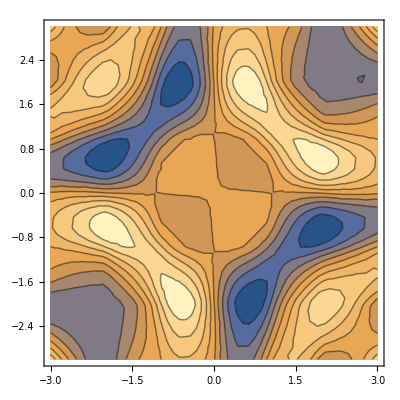

```mathematica
ContourPlot[uval[x,y],{x,-3,3},{y,-3,3}]
```

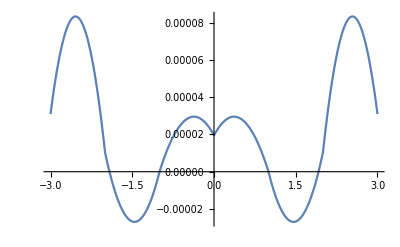

```mathematica
Plot[uval[0,y],{y,-3,3}]
```

```mathematica
Plot[uval[x,0],{x,-3,3}]
```

-Graphics-

```mathematica
(* Black hole mass operator M interms of x and y oscillators with mass 1 *)
```

```mathematica
uval=NDSolveValue[{-.5D[u[x,y],{x,2}]-.5D[u[x,y],{y,2}]+.5(x^2+y^2-2) u[x,y]- D[u[x,y],{x,1},{y,1}]-x y u[x,y]==0,u[x,-10]==u[x,10]==u[-10,y]==u[10,y]==.1},u,{x,-10,10},{y,-10,10}]
```

InterpolatingFunction[…]

```mathematica
Plot3D[uval[x,y],{x,-8,8},{y,-8,8},PlotRange->All,AxesLabel->Automatic,PlotPoints->100]
```

-Graphics3D-

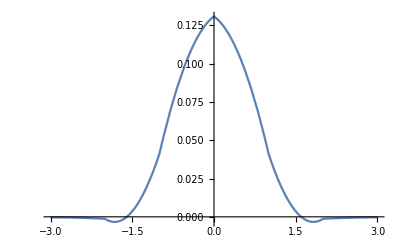

```mathematica
Plot[uval[x,0],{x,-3,3}]
```

```mathematica
Plot[uval[0,y],{y,-3,3}]
```

-Graphics-

```mathematica
(* Black hole mass 4 *)

uval=NDSolveValue[{-.5D[u[x,y],{x,2}]-.5D[u[x,y],{y,2}]+.5(x^2+y^2-8) u[x,y]- D[u[x,y],{x,1},{y,1}]-x y u[x,y]==0,u[x,-10]==u[x,10]==u[-10,y]==u[10,y]==.1},u,{x,-10,10},{y,-10,10}]
```

InterpolatingFunction[…]

```mathematica
Plot3D[uval[x,y],{x,-8,8},{y,-8,8},PlotRange->All,AxesLabel->Automatic,PlotPoints->100]
```

-Graphics3D-

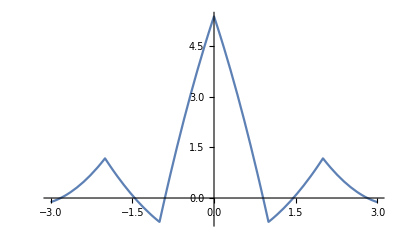

```mathematica
Plot[uval[x,0],{x,-3,3}]
```

```mathematica
Plot[uval[0,y],{y,-3,3}]
```

-Graphics-